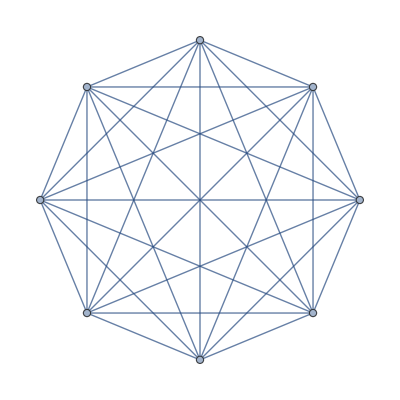

```mathematica
Graph[{Tristram<->AlphaCentauri,Tristram<->Snowdin,Tristram<->Tambi,Tristram<->Faerun,Tristram<->Norrath,Tristram<->Straylight,Tristram<->Arbre,AlphaCentauri<->Snowdin,AlphaCentauri<->Tambi,AlphaCentauri<->Faerun,AlphaCentauri<->Norrath,AlphaCentauri<->Straylight,AlphaCentauri<->Arbre,Snowdin<->Tambi,Snowdin<->Faerun,Snowdin<->Norrath,Snowdin<->Straylight,Snowdin<->Arbre,Tambi<->Faerun,Tambi<->Norrath,Tambi<->Straylight,Tambi<->Arbre,Faerun<->Norrath,Faerun<->Straylight,Faerun<->Arbre,Norrath<->Straylight,Norrath<->Arbre,Straylight<->Arbre},EdgeWeight->{34,100,63,108,111,89,132,4,79,44,147,133,74,105,95,48,88,7,68,134,107,40,11,66,144,115,135,127}]
```

```mathematica
FindHamiltonianPath[-Graphics-]
```

{Tambi,Arbre,Snowdin,AlphaCentauri,Tristram,Straylight,Faerun,Norrath}

```mathematica
GraphDistance[-Graphics-,Tambi, Arbre]+ GraphDistance[-Graphics-, Arbre, Snowdin]+ GraphDistance[-Graphics-,Snowdin, AlphaCentauri]+ GraphDistance[-Graphics-,AlphaCentauri, Tristram]+GraphDistance[-Graphics-,Tristram, Straylight]+ GraphDistance[-Graphics-,Straylight, Faerun]+ GraphDistance[-Graphics-,Faerun, Norrath]
```

251.